```mathematica
(* Computational Methods Lab 6 *) 

(*Data of Pendellum*)
b = 0;
MOI = 9000; 
fD = 0; 
rCM = 15; 
mass = 30;
g = 9.81; 
w0 = 0; 
theta0 = 1; 
angularFrequency = 0.66;
t0 = 0; 
alpha0 = (-((rCM*mass*g*Sin[theta0])) - ((((rCM)^2)*b*w0)) + ( (rCM*fD*Sin[angularFrequency])*t0))/MOI;
```

```mathematica
(*Initial Conditions*)
w0 = 0;
t0 = 0; 
theta0 = 1; 
deltaT = 0.02; 
x0 = Sin[theta0];
Energy0 = 0.5MOI*w0^2 + mass*g*30*(1-Cos[theta0]); 

(*Starting Values*)
w = w0; 
theta= theta0;
alpha = alpha0; 
x = x0; 
Energy = Energy0;

(*listOfPoints*) 
allData= List[{t0,w,theta,alpha,x,Energy}];

(*limits of iterations *) 
tmin = 0;
tmax = 20;

(*setup iterations*) 

Do [    wPlus = w + alpha*deltaT;
	thetaPlus = theta + wPlus*deltaT; 
w= wPlus;
theta = thetaPlus; 
x = Sin[theta];
Energy = (0.5*MOI*((rCM*w)^2)) +(mass*g* 30*(1-Cos[thetaPlus]));
alpha = (-((rCM*mass*g*Sin[thetaPlus]))- (((rCM^2)*b*wPlus)) + ( (rCM*fD*Sin[angularFrequency*t])))/MOI;
allData = AppendTo[allData, {t,w, theta,alpha,x,Energy}],
{t,tmin,tmax,deltaT}]; 
	allData;
```

0

```mathematica
(* t,w, theta,alpha,x,Energy *)
thetaTime = Drop[allData,None, {2,2}];
thetaTime = Drop[thetaTime,None, {3,3}];
thetaTime  = Drop[thetaTime, None,{3,3}];
thetaTime  = Drop[thetaTime, None,{3,3}];

xTime = Drop[allData, None, {2,4}];
xTime = Drop[xTime, None, {3,3}];

ETime = Drop[allData, None, {2,5}];



p1=ListPlot[xTime,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{"t(s)","x(m)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
p2=ListPlot[ETime,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t(s)","Energy(J)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
p2=ListPlot[thetaTime,PlotRange->All,PlotLabel -> ("Simple Pendellum, no drag force and no driving force"), Joined->True,Frame->True,FrameLabel->{"t(s)","Theta(Rad)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[allData, None, {2, 2}].

Drop::drop: Cannot drop positions 3 through 3 in allData.

Drop::drop: Cannot drop positions 3 through 3 in None.

Drop::normal: Nonatomic expression expected at position 1 in Drop[allData, None, {2, 4}].

Drop::drop: Cannot drop positions 3 through 3 in allData.

Drop::normal: Nonatomic expression expected at position 1 in Drop[allData, None, {2, 5}].

ListPlot::lpn: Drop[Drop[allData, None, {2, 4}], None, {3, 3}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[Drop[Drop[allData,None,{2,4}],None,{3,3}],PlotRange→All,Joined→True,Frame→True,FrameLabel→{t(s),x(m),,},LabelStyle→FontSize→14,PlotStyle→-Graphics-]

ListPlot::lpn: Drop[allData, None, {2, 5}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[Drop[allData,None,{2,5}],PlotRange→All,Joined→True,Frame→True,FrameLabel→{t(s),Energy(J),,},LabelStyle→FontSize→14,PlotStyle→-Graphics-]

ListPlot::lpn: Drop[Drop[Drop[Drop[allData, None, {2, 2}], None, {3, 3}], None, {3, 3}], None, {3, 3}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[Drop[Drop[Drop[Drop[allData,None,{2,2}],None,{3,3}],None,{3,3}],None,{3,3}],PlotRange→All,PlotLabel→Simple Pendellum, no drag force and no driving force,Joined→True,Frame→True,FrameLabel→{t(s),Theta(Rad),,},LabelStyle→FontSize→14,PlotStyle→-Graphics-]

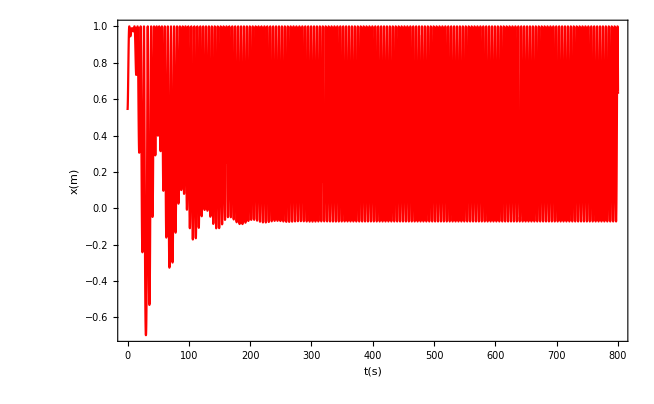
```mathematica
-Graphics-
(* Position vs time  with drag coefficient 1*) 
(* The pendellum is not in in a steady state as the position vs time graph shows that there is no pattern
```

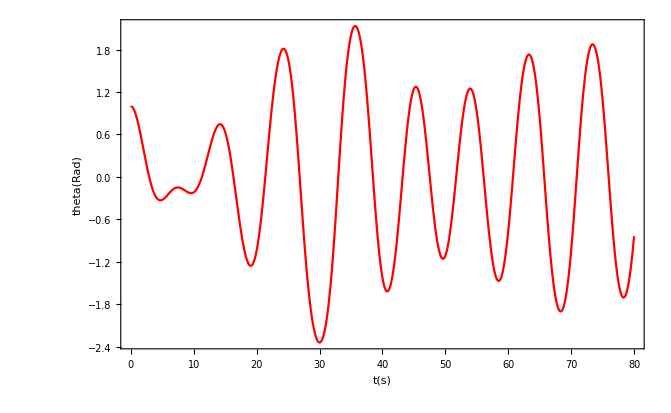
```mathematica
-Graphics-(* Air resistance and Driving Force *)
```

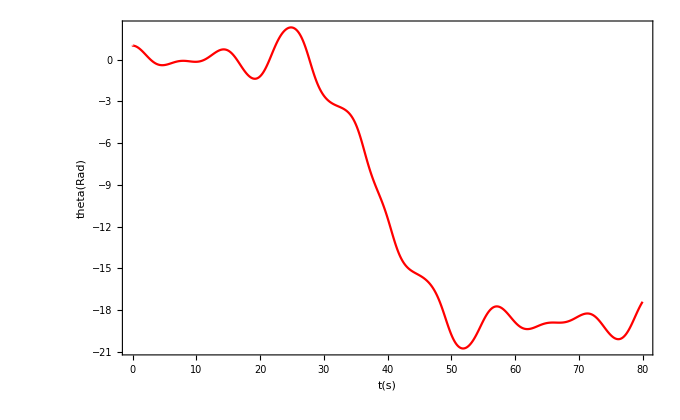
```mathematica
-Graphics-(* Driving Force with no air resistance *)
```

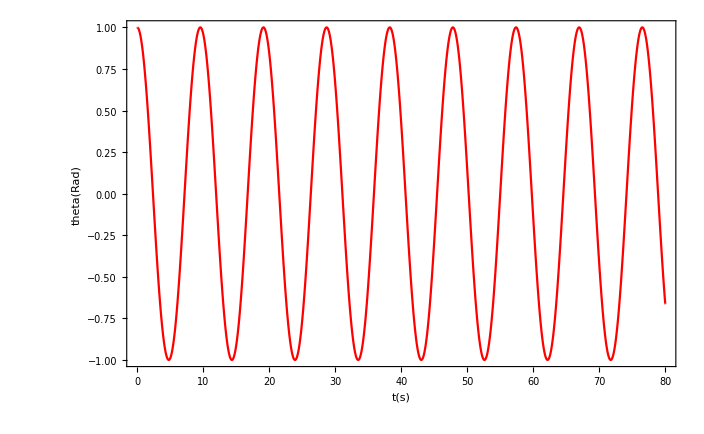
```mathematica
-Graphics-(* No air resistance and No driving Force *)
```

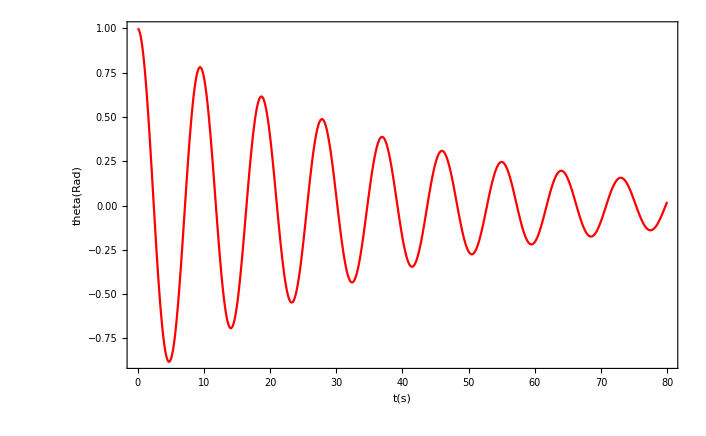
```mathematica
-Graphics-(* Air resistance and No driving Force *)
```